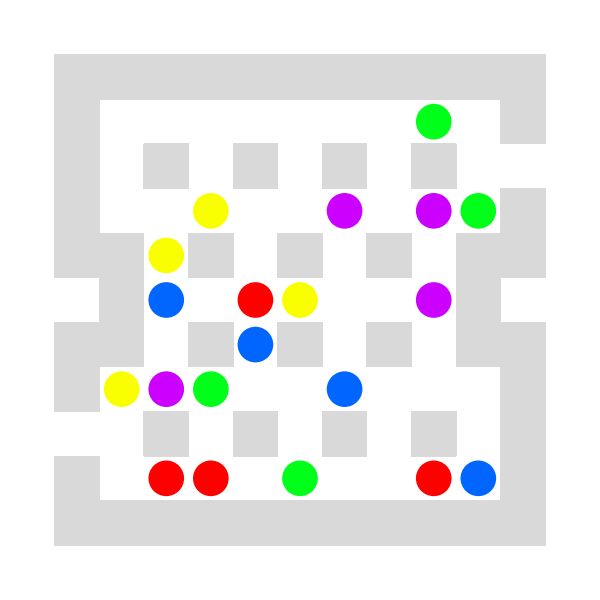

-Graphics-

-Graphics-

```mathematica
A=({{1, 1, 0, 1, 1, 0, 1, 1, 1, 1, 1}, {1, 0, 0, 0, 1, 1, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 1, 1, 0, 0, 0, 1}, {1, 1, 1, 1, 1, 0, 1, 1, 0, 1, 1}});
```

```mathematica
col[1]=Hue[0];
col[2]=Hue[.17];
col[3]=Hue[.35];
col[4]=Hue[.6];
col[5]=Hue[.8];
```

```mathematica
pic[L_]:=Graphics[{LightGray,Map[Rectangle[#-{1,1},#]&,Position[A,1,2]],Black,AbsoluteThickness[3],
Map[{col[#[[2]]],Disk[#[[1]]-{1/2,1/2},.4]}&,bird],Line[Map[#-{1/2,1/2}&,L]]},ImageSize->150]
```

```mathematica
picnopath[L_]:=Graphics[{LightGray,Map[Rectangle[#-{1,1},#]&,Position[A,1,2]],Black,
Map[{col[#[[2]]],Disk[#[[1]]-{1/2,1/2},.4]}&,bird]},ImageSize->150]
```

```mathematica
AA=Position[A,0,2];
paths={};
stack={{{1,3}}};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
last=Last[cur];
If[last=={11,9},AppendTo[paths,cur]];
pos=Complement[Intersection[Map[last+#&,{{1,0},{-1,0},{0,1},{0,-1}}],AA],cur];
If[Length[pos]>0,stack=Join[stack,Map[Append[cur,#]&,pos]]]
]
```

```mathematica
Length[paths]
```

4427

```mathematica
possibles={{2,4},{2,10},{3,2},{3,4},{3,5},{3,6},{3,7},{3,8},{3,10},{4,2},{4,3},{4,4},{4,6},{4,8},{4,9},{4,10},{5,2},{5,4},{5,5},{5,6},{5,7},{5,8},{5,10},{6,2},{6,3},{6,4},{6,6},{6,8},{6,9},{6,10},{7,2},{7,4},{7,5},{7,6},{7,7},{7,8},{7,10},{8,2},{8,3},{8,4},{8,6},{8,8},{8,9},{8,10},{9,2},{9,4},{9,5},{9,6},{9,7},{9,8},{9,10},{10,2},{10,8}};
```

```mathematica
d[x_,y_]:=(x-y).(x-y)
```

```mathematica
d[L_]:=Min[Flatten[Table[d[L[[i]],L[[j]]],{i,1,Length[L]-1},{j,i+1,Length[L]}]]]
```

```mathematica
randomizebirds:=(bird={{{0,0},0}};
For[n=1,n≤numspecies,n++,
For[k=1,k≤numbirds,k++,
temp=possibles[[RandomInteger[{1,53}]]];
same=Select[bird,#[[2]]==n&];samebirds=If[same=={},{},Transpose[same][[1]]];
While[MemberQ[Transpose[bird][[1]],temp]||(d[Append[samebirds,temp]]==1&&birdsonpath==1),temp=possibles[[RandomInteger[{1,53}]]]];
AppendTo[bird,{temp,n}]]];bird=Rest[bird];)
```

```mathematica
countbirds[L_]:=Module[{},
c[1]=0;c[2]=0;c[3]=0;c[4]=0;c[5]=0;
For[ii=1,ii≤Length[L],ii++,
For[jj=1,jj≤numspecies*numbirds,jj++,
If[L[[ii]]==bird[[jj,1]],c[bird[[jj,2]]]++]]];
Array[c,numspecies]]
```

```mathematica
numspecies=5;
numbirds=3;
birdsonpath=1;
```

```mathematica
For[p=1,p>0,p++,
randomizebirds;
s=Select[paths,countbirds[#]==Table[birdsonpath,{numspecies}]&];
(*Print[Length[s]];*)
If[Length[s]==1,Print[picnopath[s[[1]]]];Print[pic[s[[1]]]]]]
```

$Aborted

## through 1

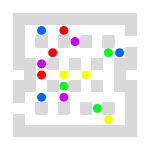

-Graphics-

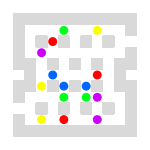

-Graphics-

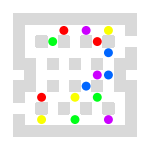

-Graphics-

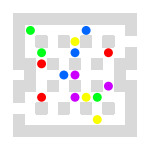

-Graphics-

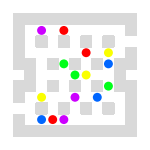

-Graphics-

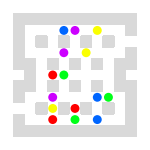

-Graphics-

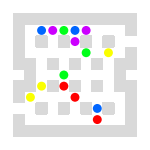

-Graphics-

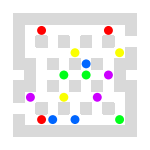

-Graphics-

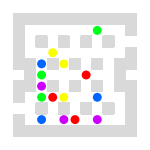

-Graphics-

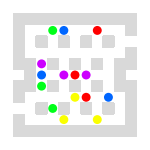

-Graphics-

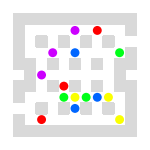

-Graphics-

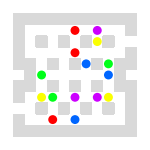

-Graphics-

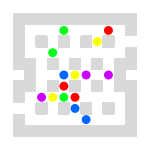

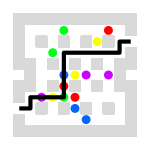

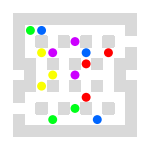

-Graphics-

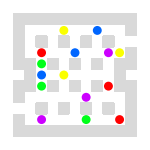

-Graphics-

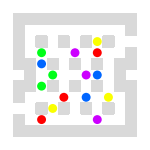

-Graphics-

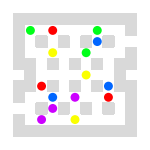

-Graphics-

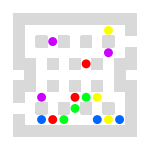

-Graphics-

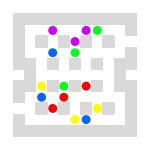

-Graphics-

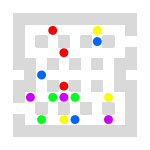

-Graphics-

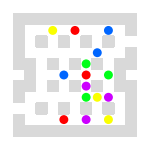

-Graphics-

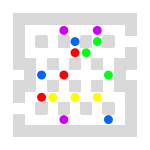

-Graphics-

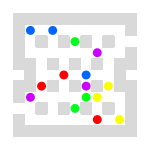

-Graphics-

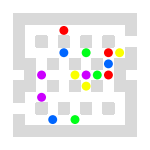

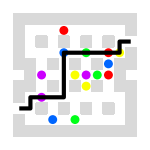

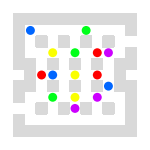

-Graphics-

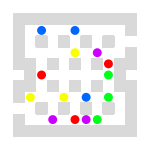

-Graphics-

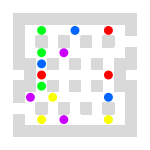

-Graphics-

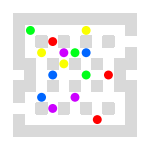

-Graphics-

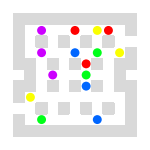

-Graphics-

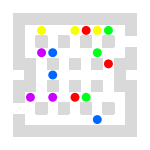

-Graphics-

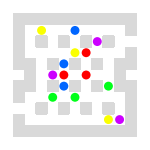

-Graphics-

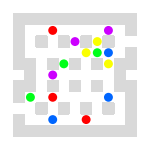

-Graphics-

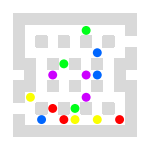

-Graphics-

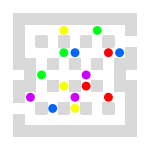

-Graphics-

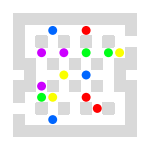

-Graphics-

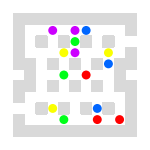

-Graphics-

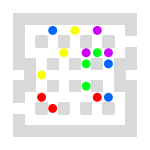

-Graphics-

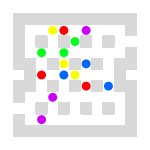

-Graphics-

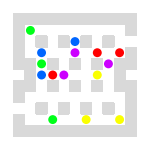

-Graphics-

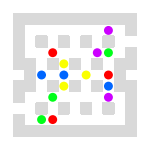

-Graphics-

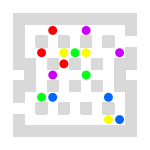

-Graphics-

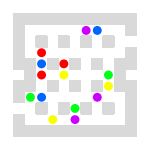

-Graphics-

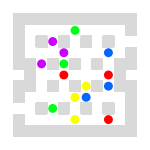

-Graphics-

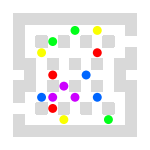

-Graphics-

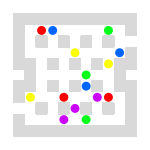

-Graphics-

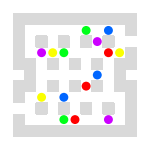

-Graphics-

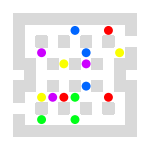

-Graphics-

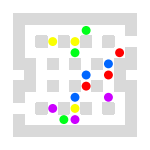

-Graphics-

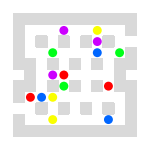

-Graphics-

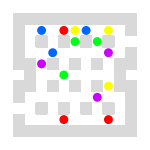

-Graphics-

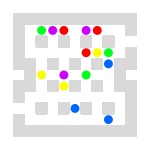

-Graphics-

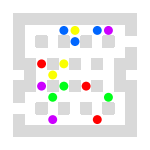

-Graphics-

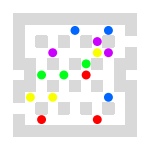

-Graphics-

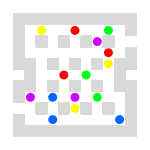

-Graphics-

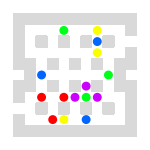

-Graphics-

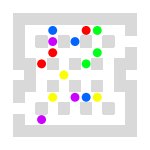

-Graphics-

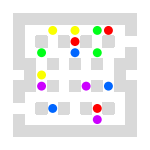

-Graphics-

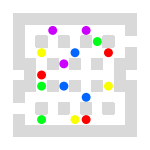

-Graphics-

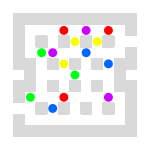

-Graphics-

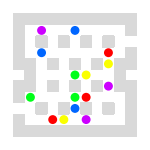

-Graphics-

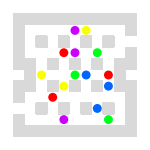

-Graphics-

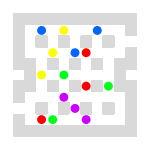

-Graphics-

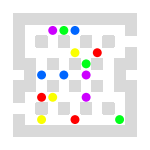

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## through 2

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## through 3

-Graphics-

-Graphics-

-Graphics-

«23 more identical outputs»

## through 4

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»